# Genetic Algorithms Code - Growth Data

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[ListInterpolation::inhr];
ParallelEvaluate@Off[General::munfl];
```

### Various Constants

```mathematica
(* Planck18 Values and other constants *)
obh2pl = 0.02237;
obh2plerr = 0.00015;
ompl = 0.3153;
omplerr = 0.0073;
σ8pl = 0.8111;
σ8err = 0.0060;
h0pl = 0.6736;
h0riess = 73.04/100;
Tcmb=2.7255;
c = 299792.458;
cH0=2997.92458;
```

## Genetic Algorithms Theory

### Genetic Algorithms Basics

```mathematica
poly[x_]:=x
polyxtox[x_]:=x^x
polyCPL[x_]:=x/(1+x)
polya[x_]:=(1/(1+x))^3
(* grammar={poly,Exp,Sin,Cos,Tan,Log};*)
grammar={poly};
(* Expression length *)
length=4;
depth=4;
rang1={-1,1};
rang2={1,Length[grammar]};
rang3={0,1};
rang4={0,9};
toursize=4;
selectionrate=0.3;
```

```mathematica
func[x_,kid_,gram_]:=Sum[kid[[i,1]] (gram[[kid[[i,2]]]]@(kid[[i,3]] x))^kid[[i,4]],{i,1,length}]
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]};
mut=Which[rep[[2]]==1,RandomReal[rang1],rep[[2]]==2,RandomInteger[rang2],rep[[2]]==3,RandomReal[rang3],rep[[2]]==4,RandomReal[rang4]];
ReplacePart[kid,rep->mut]]
cross[{kid1_,kid2_}]:=Module[{len},len=RandomInteger[{1,length-1}];
{Join[kid1[[1;;len]],kid2[[(len+1);;-1]]],Join[kid1[[(len+1);;-1]],kid2[[1;;len]]]}]
```

```mathematica
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[1,2]]
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[-1,2]]
```

```mathematica
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2];
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={};
chromosomes=ParallelTable[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomReal[rang4]},{pop},{length}];
t1=AbsoluteTime[];
Do[pigs=func[x,#,grammar]&/@chromosomes;
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[chi2[pigs[[j]]],.5],10^7],j},{j,1,Length[pigs]}],#1[[1]]>#2[[1]]&];AppendTo[bestfitperstep,{fitness[[1,1]],pigs[[fitness[[1,2]]]],chromosomes[[fitness[[1,2]]]]}];p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes[[p2[[jj,1]]]], chromosomes[[p2[[jj,2]]]]}],{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes[[p2[[jj,1]]]]],mutation[chromosomes[[p2[[jj,2]]]]]},{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,
Print["Time taken: ",AbsoluteTime[]-t1," sec"];
Print["χ_min^2 = ",Abs[fitness[[1,1]]]];
Print["Best-fit function is: "];
Print[bestfitperstep[[-1,2]]];
Speak["The end"];];
bestfitperstep]
```

## Real Data Analysis - ΛCDM Model

### Basic Functions for the wCDM Model

```mathematica
(* Note that in the dynamical data case we use directly the analytical expressions for the wCDM instead of the nCPL model that we did in the background data. This choice does not affect the overall results, since we only use them for the ΛCDM case. *)
Hwcdm[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)));
(* Growth for wCDM models *)
δ[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δ[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δ[a,w,Ω]/δ[1,w,Ω]
dAh[a_,om_,w_]:=(2a)/(√om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)]);
```

### Growth data

#### Import the Growth Compilation

```mathematica
datagrowth=Import["./data/growth_data_2022.txt","Table"][[2;;-1]]/.{z_,fs8_,sfs8_,om_}->{(1/(1+z)),fs8,sfs8,om};
datagrowthres=Import["./data/growth_data_2022.txt","Table"][[2;;-1]]/.{z_,fs8_,sfs8_,om_}->{(1/(1+z))^3,fs8/(1/(1+z)),sfs8/(1/(1+z)),om};
ndatgrowth=Length[datagrowth]
```

20

#### χ^2 of Growth

```mathematica
(* Add support for WiggleZ and eBOSS data Cij *)
Cijwigglez=Import["./data/Cij_WiggleZ.txt","Table"];
CijeBOSS=Import["./data/sdss_DR12_LRG_FSBAO_DMDHfs8_covtot.txt","Table"][[{3,6},{3,6}]];
```

```mathematica
(* Support term for WiggleZ and SDSS Cij *)
Wigglez={4,5,6};
eBOSS={16,17};
Cijfs8=DiagonalMatrix[datagrowth[[All,3]]^2];
Cijfs8[[Wigglez,Wigglez]]=Cijwigglez;
Cijfs8[[eBOSS,eBOSS]]=CijeBOSS;
InvCijfs8=Inverse[Cijfs8];
(* Fiducial Subscript[Ω, m] from paper *)
omf=datagrowth[[All,4]];
```

```mathematica
(* Corrections due to the fiducial cosmology *)
ratiogrowth[a_,om_,w_,omfid_]:=((Hwcdm[a,w,om]dAh[a,om,w])/(Hwcdm[a,-1,omfid] dAh[a,omfid,-1]));
(* χ^2 correlated term *)
vecgrowth[om_,w_,σ8_]:=Table[datagrowth[[i,2]]-fσ8wCDM[datagrowth[[i,1]],w,om,σ8]/ratiogrowth[datagrowth[[i,1]],om,w,omf[[i]]],{i,1,ndatgrowth}]
chi2growth[om_,w_,σ8_]:=vecgrowth[om,w,σ8].InvCijfs8.vecgrowth[om,w,σ8]
```

#### Growth Data - Maximum Likelihood Method for ΛCDM

```mathematica
mingrowth=FindMinimum[chi2growth[om,-1,σ8],{om,0.3,0.31},{σ8,0.8,0.81}];
ombfgrowth=mingrowth[[2,1,2]];
σ8bfgrowth=mingrowth[[2,2,2]];
chifungrowth=ListInterpolation[ParallelTable[chi2growth[om,-1,σ8],{om,ombfgrowth-0.02,ombfgrowth+0.02,0.02},{σ8,σ8bfgrowth-0.02,σ8bfgrowth+0.02,0.02},DistributedContexts->Automatic],{{ombfgrowth-0.02,ombfgrowth+0.02},{σ8bfgrowth-0.02,σ8bfgrowth+0.02}}];
(* Params that we want to calculate the errors *)
paramsgrowth={om,σ8};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fijgrowth=1/2 Table[D[chifungrowth[om,σ8],paramsgrowth[[p]],paramsgrowth[[d]]]/.mingrowth[[2]],{p,1,Length[paramsgrowth]},{d,1,Length[paramsgrowth]}];
cijgrowth=Inverse[Fijgrowth];
errorsgrowth=Sqrt[Diagonal[cijgrowth]];
Print["The best fit parameter for Ω_(0  m) and σ_8 is: Ω_(0  m)=",ombfgrowth,"±",errorsgrowth[[1]]," and σ_8=",σ8bfgrowth,"±",errorsgrowth[[2]]," with a χ^2 value: χ^2=",mingrowth[[1]]]
```

The best fit parameter for Ω_(0  m) and σ_8 is: Ω_(0  m)=0.260162±0.0339953 and σ_8=0.823308±0.0355267 with a χ^2 value: χ^2=16.0608

## Genetic Algorithms

### Genetic Algorithms Theory

#### Specific χ^2 Functions - GA

```mathematica
H0GA=67.17004414248437;
hGA=H0GA/100;
HGA[a_]:=H0GA√(1+x (-0.8999883844902956+0.2620381909322407 (1+0.15327819800211584 x)^3-0.381979946511561 (1+1.6189955164319452 x))^2)/.x->1/a-1
dAGA[a_]:=cH0/hGA x (1+(0.8718351321839224-0.12885030729521135 x)^2 x)/(1+x)^2/.x->1/a-1
```

```mathematica
(* Corrections due to the fiducial cosmology *)
ratioGA[a_,omfid_]:=((HGA[a]dAGA[a])/(100cH0 Hwcdm[a,-1,omfid] dAh[a,omfid,-1]));
(* χ^2 for GA *)
chi2GA[fs8GA_,data_]:=Module[{V,yi,ythi},
yi=data[[All,2]];
ythi=Table[(fs8GA/.x->data[[i,1]])/ratioGA[data[[i,1]],omf[[i]]],{i,1,Length[data]}];
(yi-ythi).InvCijfs8.(yi-ythi)
]
(* χ^2 for GA *)
chi2GAmarg[fs8GA_,data_]:=Module[{A,B,Γ,yi,ythi},
yi=data[[All,2]];
ythi=Table[(fs8GA/.x->data[[i,1]])/ratioGA[data[[i,1]],omf[[i]]],{i,1,Length[data]}];
A=yi.InvCijfs8.yi;
B=yi.InvCijfs8.ythi+ythi.InvCijfs8.yi;
Γ=ythi.InvCijfs8.ythi;
A-B^2/(4Γ)]
offsetGA[fs8GA_,data_]:=Module[{A,B,Γ,yi,ythi},
yi=data[[All,2]];
ythi=Table[(fs8GA/.x->data[[i,1]])/ratioGA[data[[i,1]],omf[[i]]],{i,1,Length[data]}];
B=yi.InvCijfs8.ythi+ythi.InvCijfs8.yi;
Γ=ythi.InvCijfs8.ythi;
B/(2Γ)]
chi2[fs8GA_,data_]:=Module[{temp},
temp=chi2GAmarg[fs8GA,data];If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
```

```mathematica
off=offsetGA[x(1+x),datagrowth]
chi2GA[off x(1+x),datagrowth]
chi2GAmarg[x(1+x),datagrowth]
```

0.283262

153.848

153.848

```mathematica
(* end *)
```

### Genetic Algorithms Calculations

#### Main Loop

```mathematica
t1=AbsoluteTime[];
generations=200;
Nseed=3;
Ncross=3;
Nmut=3;
prog`int=0;
prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,Nseed Ncross Nmut}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
Do[GApop[jj,kk,nn]=GAevo[1234jj,generations,100,0.65+0.05kk,0.20+0.05nn,False];prog`pop++;prog`int=0;,{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}];
Print["Time Taken: ",(AbsoluteTime[]-t1)/60," minutes"]
```

Time Taken: 11.34537727 minutes

```mathematica
Rasterize[ListLogLogPlot[Partition[Flatten[Table[GApop[jj,kk,nn][[All,1]]//Abs,{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}]],generations],Joined->True,PlotRange->{5,10^5},Frame->True,FrameStyle->Black,Epilog->{Dashed,Line[{{0.1,mingrowth[[1]]},{generations,mingrowth[[1]]}}//Log]},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14,PlotLegends->Automatic],ImageSize->400,RasterSize->1000]
```

```mathematica
chi2minGA=Partition[Flatten[Table[{jj,kk,nn,GApop[jj,kk,nn][[-1,1]]},{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}]],4];
SortBy[chi2minGA,Last]//Reverse
```

{{3,1,1,-9.02058},{2,3,3,-9.07562},{3,2,3,-9.10004},{3,1,3,-9.10773},{3,2,1,-9.14531},{1,1,3,-9.19092},{2,2,2,-9.22011},{2,1,2,-9.23971},{2,1,3,-9.24798},{2,1,1,-9.25827},{3,3,2,-9.26261},{2,3,1,-9.26596},{1,2,3,-9.28234},{2,3,2,-9.31032},{1,1,1,-9.323},{3,2,2,-9.33484},{1,1,2,-9.34024},{1,2,1,-9.34773},{1,3,3,-9.34813},{3,1,2,-9.35517},{1,3,2,-9.36302},{1,2,2,-9.39},{1,3,1,-9.4037},{2,2,1,-9.46692},{2,2,3,-9.50252},{3,3,3,-9.51585},{3,3,1,-9.57741}}

```mathematica
GApop[3,1,1][[-1,2]]
```

-0.135454 x^0.116615-0.0265704 x^4.25321-0.0615598 x^6.738+0.116765 x^7.83758

```mathematica
fs8GA0[x_]:=-0.13545441748838594 x^0.1166154660109413-0.026570364365728412 x^4.253207425004835-0.0615597905827236 x^6.7380047741634215+0.11676490228909535 x^7.837581287263632
(* χ^2 correlated term *)
vecGA[fs8GA_]:=Table[datagrowth[[i,2]]-(fs8GA/.x->datagrowth[[i,1]])/ratioGA[datagrowth[[i,1]],omf[[i]]],{i,1,Length[datagrowth]}]
chi2GA[fs8GA_]:=vecGA[fs8GA].InvCijfs8.vecGA[fs8GA]
FindMinimum[chi2GA[fs8c fs8GA0[x]],{fs8c,1.1,1.11}]
```

{9.02058,{fs8c→-3.50887}}

```mathematica
fs8c0=-3.5088657376306034;
fs8GA[x_]:=fs8c0 fs8GA0[x]
```

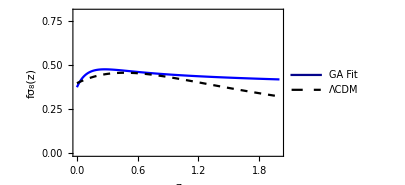

```mathematica
col=GrayLevel[0.3,0.2];
plt1=Plot[{fs8GA[1/(1+z)]//Evaluate,fσ8wCDM[1/(1+z),-1,ombfgrowth,σ8bfgrowth]},{z,0,2},PlotStyle->{Blue,{Black,Dashed}},Frame->True,ImageSize->300,FrameLabel->{"z","fσ_8(z)"},PlotRange->{All,{0,0.8}},FrameStyle->Black,BaseStyle->FontSize->16,PlotLegends->Placed[LineLegend[{RGBColor["#04048c"],Dashed},{"GA Fit","ΛCDM"}],Scaled[{0.8,0.8}]],Axes->None]
```

```mathematica
(* end *)
```

#### Derived Results

```mathematica
(* The results are presented in the form {Subscript[d, L](x), H(x), # of sample} *)
fGAdistro=Table[{GApop[jj,kk,nn][[-1,2]],GApop[jj,kk,nn][[-1,1]],jj,kk,nn},{jj,1,Nseed },{kk,1,Ncross},{nn,1,Nmut}]
chi2tab=Table[{GApop[jj,kk,nn][[-1,1]]//Abs,jj,kk,nn},{jj,1,Nseed },{kk,1,Ncross},{nn,1,Nmut}]
Select[chi2tab,#[[1]]<mingrowth[[1]]&]
```

```mathematica
chi2minGA=Partition[Flatten[Table[{jj,kk,nn,GApop[jj,kk,nn][[-1,1]]},{jj,1,Nseed},{kk,1,Ncross},{nn,1,Nmut}]],4];
SortBy[chi2minGA,Last]//Reverse
```

```mathematica
GApop[3,3,2][[-1,2]]
```

-0.0490223-0.0141108 x^3.7108+0.0215578 x^9

#### 1σ Errors

```mathematica
fs8GA0[x_]:=-0.04902230433205146-0.014110818142645466 x^3.710799385476408+0.02155779852115262 x^9
(* χ^2 correlated term *)
vecGA[fs8GA_]:=Table[datagrowth[[i,2]]-(fs8GA/.x->datagrowth[[i,1]])/ratioGA[datagrowth[[i,1]],omf[[i]]],{i,1,Length[datagrowth]}]
chi2GA[fs8GA_]:=vecGA[fs8GA].InvCijfs8.vecGA[fs8GA]
FindMinimum[chi2GA[fs8c fs8GA0[x]],{fs8c,1.1,1.11}]
```

{11.8615,{fs8c→-9.02631}}

```mathematica
fs8c0=-9.026306977414507;
fs8GA[x_]:=fs8c0 fs8GA0[x]
δfs8[x_,a1_,a2_,a3_]:=x(a1+a2 x+a3 x^2)
```

```mathematica
Dij=CholeskyDecomposition[(InvCijfs8+Transpose[InvCijfs8])/2];
yj=datagrowth[[All,2]];

fbfj=Table[fs8GA[datagrowth⟦j,1⟧]/ratioGA[datagrowth⟦j,1⟧,omf⟦j⟧],{j,1,Length[datagrowth]}];
```

```mathematica
chi2confGA[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{δfj,vec1,vec2,conf},
δfj=Table[δfs8[datagrowth⟦j,1⟧,a1,a2,a3]/ratioGA[datagrowth⟦j,1⟧,omf⟦j⟧],{j,1,Length[datagrowth]}];
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ])/Erf[1/(√2)],{i,1,Length[datagrowth]}];
Sum[(conf[[k]]-1)^2,{k,1,Length[datagrowth]}]]
```

```mathematica
chi2tot[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=chi2confGA[a1,a2,a3]+chi2[fs8GA[x]+δfs8[x,a1,a2,a3]]
```

```mathematica
fminfs8err=FindMinimum[chi2tot[a1,a2,0],{a1,0.01,0.011},{a2,0.011,0.0111}]
```

{13.1402,{a1→-0.378603,a2→0.280495}}

### Comparison with ΛCDM

#### fσ_8(z) Plot

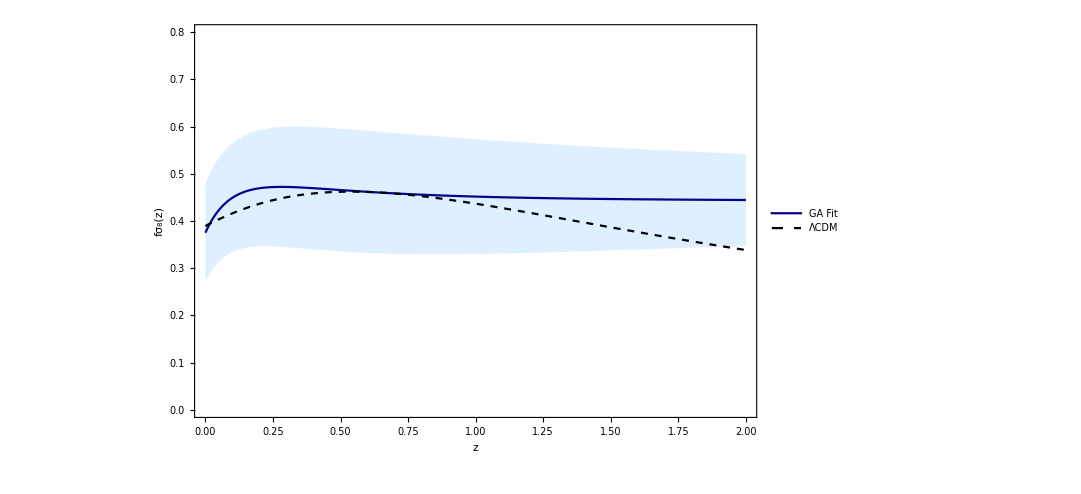

```mathematica
ϵ0={-1,0,1};
col=GrayLevel[0.3,0.2];
plt1=Plot[{fs8GA[1/(1+z)]+δfs8[1/(1+z),a1,a2,0]ϵ0/.fminfs8err[[2]]//Evaluate,fσ8wCDM[1/(1+z),-1,ombfgrowth,σ8bfgrowth]},{z,0,2},PlotStyle->{LightBlue,RGBColor["#04048c"],LightBlue,{Black,Dashed}},Filling->{1->{{3},LightBlue}},Frame->True,ImageSize->800,FrameLabel->{"z","fσ_8(z)"},PlotRange->{All,{0,0.8}},FrameStyle->Black,BaseStyle->FontSize->16,PlotLegends->Placed[LineLegend[{RGBColor["#04048c"],Dashed},{"GA Fit","ΛCDM"}],Scaled[{0.8,0.8}]],Axes->None]
```

```mathematica
datagrowthplt=Table[{1/datagrowth[[i,1]]-1,Around[datagrowth[[i,2]],datagrowth[[i,3]]]},{i,1,ndatgrowth}];
```

```mathematica
plt2=ListPlot[datagrowthplt, IntervalMarkers->"Fences"];
```

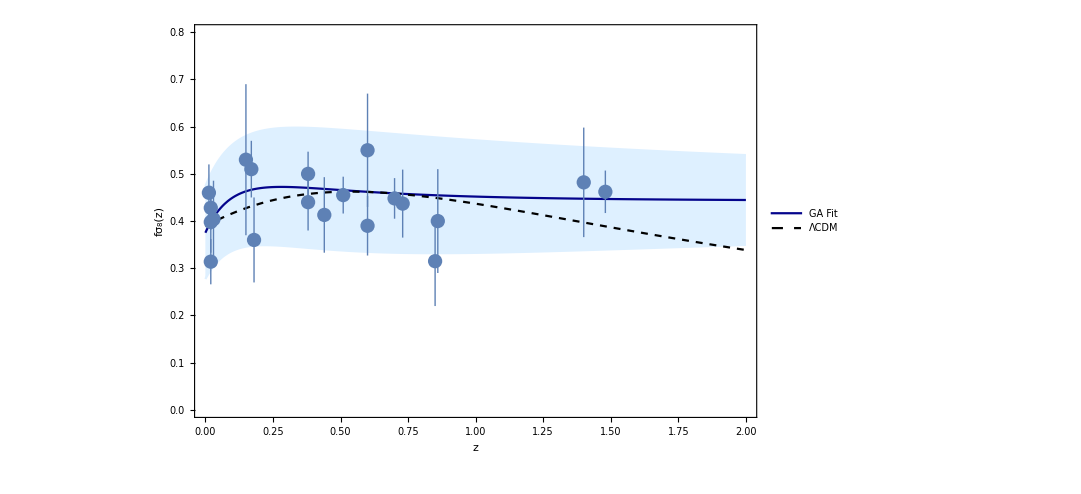

```mathematica
plt=Show[plt1,plt2]
```

```mathematica
Export[NotebookDirectory[]<>"fs8plot.pdf",plt,ImageResolution->1000];
```